```mathematica
BordersUnsorted[f_]:=Module[{edgs},
  edgs=Flatten[Map[{
   {Part[#,1],Part[#,2]},
   {Part[#,2],Part[#,3]},
   {Part[#,3],Part[#,1]},
   {Part[#,2],Part[#,1]},
   {Part[#,3],Part[#,2]},
  {Part[#,1],Part[#,3]}
  }&,f],1];
DeleteDuplicates[Flatten[Part[Select[Tally[edgs],Last[#]==1&],;;,1]]]
];

TriangleArea[tri_]:=0.5Norm[Cross[Part[tri,2]-Part[tri,1],Part[tri,3]-Part[tri,1] ]];

InverseMassMatrix[v_,f_]:=Module[{ar},
ar=ConstantArray[.0,Length[v]];
Scan[Part[ar,#]+=TriangleArea[Part[v,#]]/3&,f];
SparseArray[MapIndexed[{First[#2],First[#2]}->#1&,1./ar]]
];
```

```mathematica
AngleDefect[objfile_,returnOnlyInner_:True,normalize_:False]:=Module[{brd,inner,angleDefect,input,v,f},
input=Import[objfile,"GraphicsComplex"];
v=Part[input,1];
Clear[x];
f=Flatten[Cases[input,Triangle[x_]->x,Infinity],1];
brd=BordersUnsorted[f];
inner=Complement[Range[Length[v]],brd];
angleDefect=ConstantArray[-2π,Length[v]];

Map[Function[fi,
Table[
Module[{a,k1,k2,e1,e2},
k1=Mod[k,3]+1;
k2=Mod[k+1,3]+1;
e1=Part[v,Part[fi,k1]]-Part[v,Part[fi,k]];
e2=Part[v,Part[fi,k2]]-Part[v,Part[fi,k]];
a=ArcCos[e1.e2/ (Norm[e1] *Norm[e2])];
Part[angleDefect,Part[fi,k]] +=a;
],{k,3}]
],f];

If[normalize,angleDefect=InverseMassMatrix[v,f].angleDefect]; 

Part[angleDefect,brd]=.0;
If[returnOnlyInner,Part[angleDefect,inner],angleDefect]
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
file="./";
```

```mathematica
deg=1/Pi 180;
```

RAD:: max=0.00716394, mean=0.000552587, SD=0.000536803, Var=2.88157×10^-7

DEG:: max=0.410463, mean=0.0316609, SD=0.0307565, Var=0.0000165102

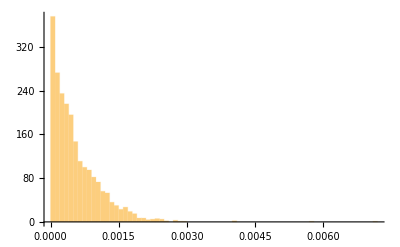

```mathematica
ad=Abs[AngleDefect[file]];

StringForm["RAD:: max=`1`, mean=`2`, SD=`3`, Var=`4`",Max[ad],Mean[ad], StandardDeviation[ad], Variance[ad]]
StringForm["DEG:: max=`1`, mean=`2`, SD=`3`, Var=`4`",Max[ad] deg,Mean[ad]deg, StandardDeviation[ad]deg, Variance[ad]deg]

Histogram[ad,PlotRange->All]
```

RAD:: max=0.0259333, mean=0.00259587, SD=0.00272927, Var=7.44893×10^-6

DEG:: max=1.48587, mean=0.148732, SD=0.156376, Var=0.000426792

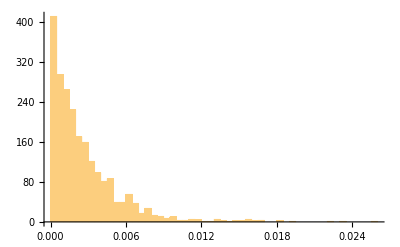

```mathematica
adNorm=Abs[AngleDefect[file, True, True]];

StringForm["RAD:: max=`1`, mean=`2`, SD=`3`, Var=`4`",Max[adNorm],Mean[adNorm], StandardDeviation[adNorm], Variance[adNorm]]
StringForm["DEG:: max=`1`, mean=`2`, SD=`3`, Var=`4`",Max[adNorm] deg,Mean[adNorm]deg, StandardDeviation[adNorm]deg, Variance[adNorm]deg]

Histogram[adNorm,PlotRange->All]
```

0.00872665

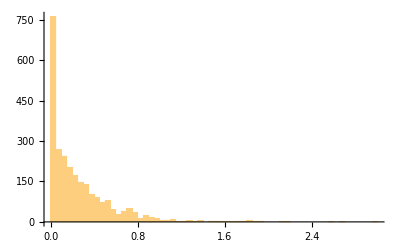

-Graphics3D-

```mathematica
thres = .5/180 Pi

adAll=Abs[AngleDefect[file,False, True]];
Histogram[adAll/thres,PlotRange->All]

input=Import[file,"GraphicsComplex"];
v=Part[input,1];
f=Flatten[Cases[input,Triangle[x_]->x,Infinity],1];
(*cl=ColorData["CherryTones"]/@(0.1+0.9Rescale[ad2]);*)
viz = Clip[adAll/thres, {0,1}];
cl=ColorData[{"CherryTones", "Reverse"}]/@(Rescale[viz]);

Graphics3D[
{
EdgeForm[],
GraphicsComplex[v,Polygon[f],VertexColors->cl]
},Boxed->False
]
```